```mathematica
SetOptions[EvaluationNotebook[],LightDark->"Light"];
SetDirectory[NotebookDirectory[]];
```

## Renormalisation

## Winding numbers

```mathematica
(* copied from Geometrical Phyllotaxis *)
euclideanWindingNumberPair[mn_] := Module[{m,n,u,v},
{{m,u},{n,v}}= euclideanMatrixProduct[mn];
{u,v}
];

eMatrix = ({
 {1, 1},
 {0, 1}
});
sMatrix=({
 {0, 1},
 {1, 0}
});

euclideanMatrixProduct[mn_] := Module[{q,res},
q = euclideanQCoefficients[mn];
res= (Map[  MatrixPower[eMatrix,#] . sMatrix &,q]);
res= If[Length[res]>0,Dot@@res,IdentityMatrix[2]];
res = sMatrix . res;

res
]/; NumericQ[First[mn]];
euclideanMatrixProduct[{1,0}] = ({
 {0, -1},
 {1, 0}
});
euclideanMatrixProduct[{0,1}] = ({
 {1, 0},
 {0, -1}
});
euclideanDelta[mn_]  := Det@euclideanMatrixProduct[mn];


euclideanQCoefficients[{m_,n_}] := Module[{r,q,i},
	i=0;
	r[-1]=n; 
	r[0] = m;
	While[r[i] > 0  , 
		q[i] = Floor[r[i-1]/r[i]];
		r[i+1] = r[i-1] - q[i]*r[i];
		i++;
	];
 Table[q[j],{j,0,i-1}]
];
```

## Example

```mathematica
ffs=Directive[FaceForm[Lighter@StandardGreen],EdgeForm[Gray]];
```

```mathematica
algebraicForms[m_,n_,u_,v_,s_,θ_,Δ_] := Module[{z1,zm,zn,pm,pn,renormalisation,h,d,gamma,DeltaIs,GammaIs,hWithGamma,dWithGamma,dAxisRange},
DeltaIs = { -n u+m v -> Δ, n u - m v -> -Δ, Δ^2->1};
gamma=n^2+m^2 s^2-2 m n s Cos[θ];
GammaIs = {gamma-> Γ};
z1=  (v-s u Cos[θ]-ⅈ s u Sin[θ])/(n-m s Cos[θ]-ⅈ m s Sin[θ]);
zm=  Δ*(m z1 - u) ;
zn= Δ*(n z1- v);
pm=Simplify@ComplexExpand[ReIm[zm]];
pm = pm //. DeltaIs;
pn=Simplify@ComplexExpand[ReIm[zn]];
pn = pn //. DeltaIs;
renormalisation= RotationTransform[Arg[zm]]@* ScalingTransform[Abs[zm]*{1,1}];
h= Simplify[Simplify@ComplexExpand[Im[z1]]//. DeltaIs  /. v->(n u+Δ)/m];
d= Simplify@ComplexExpand[Re[z1]]//. DeltaIs ;
Which[
TrueQ[s==1],
	dAxisRange= {},
ResourceFunction["SymbolQ"][s],
	dAxisRange={Limit[d,s->∞],d/. s->0},
True,
	dAxisRange=Missing[]
];
hWithGamma=h/. GammaIs;
dWithGamma=d/. GammaIs;
<|
"z1"->z1
,
"zm" ->  zm
,
"zn"-> zn
,"pm"->pm,"pn"->pn
,"tanAlpham"->pm[[2]]/pm[[1]],"tanAlphan"->pn[[2]]/pn[[1]],
"renormalisation"->renormalisation
,"h"->h,"d"->d,"Γ"->gamma
,"hGamma"->hWithGamma,"dGamma"->dWithGamma
,"dAxisRange"->dAxisRange
|>
];
```

### General case

```mathematica
Clear[m,n,u,v,s,θ,Δ,Γ];
af=KeyDrop[algebraicForms[m,n,u,v,s,θ,Δ],{"renormalisation"}];
af["pm"]* af["Γ"]// TeXForm
af["pn"]* af["Γ"]// TeXForm
```

\{-s (m s-n \cos (\theta )),n s \sin (\theta )\}

```mathematica
Simplify[af["Γ"]*Together[af["pm"].af["pm"]]]
```

1

```mathematica
Simplify[Together[af["pm"]. af["pm"]]]
```

1/(n^2+m^2 s^2-2 m n s Cos[θ])

### Orthogonal

```mathematica
of=KeyDrop[algebraicForms[m,n,u,v,s,π/2,Δ],{"renormalisation"}];
of 
Map[TeXForm,of]
```

<|z1→(-ⅈ s u+v)/(n-ⅈ m s),zm→(-u+(m (-ⅈ s u+v))/(n-ⅈ m s)) Δ,zn→(-v+(n (-ⅈ s u+v))/(n-ⅈ m s)) Δ,pm→{n/(n^2+m^2 s^2),(m s)/(n^2+m^2 s^2)},pn→{-(m s^2)/(n^2+m^2 s^2),(n s)/(n^2+m^2 s^2)},tanAlpham→(m s)/n,tanAlphan→-n/(m s),h→(s Δ)/(n^2+m^2 s^2),d→(m s^2 u+n v)/(n^2+m^2 s^2),Γ→n^2+m^2 s^2,hGamma→(s Δ)/Γ,dGamma→(m s^2 u+n v)/Γ,dAxisRange→{u/m,v/n}|>

<|z1→\frac{v-i s u}{n-i m s},zm→\Delta  \left(-u+\frac{m (v-i s u)}{n-i m s}\right),zn→\Delta  \left(-v+\frac{n (v-i s u)}{n-i m s}\right),pm→\left\{\frac{n}{m^2 s^2+n^2},\frac{m s}{m^2 s^2+n^2}\right\},pn→\left\{-\frac{m s^2}{m^2 s^2+n^2},\frac{n s}{m^2 s^2+n^2}\right\},tanAlpham→\frac{m s}{n},tanAlphan→-\frac{n}{m s},h→\frac{\Delta  s}{m^2 s^2+n^2},d→\frac{m s^2 u+n v}{m^2 s^2+n^2},Γ→m^2 s^2+n^2,hGamma→\frac{\Delta  s}{\Gamma },dGamma→\frac{m s^2 u+n v}{\Gamma },dAxisRange→\left\{\frac{u}{m},\frac{v}{n}\right\}|>

```mathematica
circleMidPoint=Mean[of["dAxisRange"]]
```

1/2 (u/m+v/n)

```mathematica
Together[Expand[Together[Simplify[(of["d"]-circleMidPoint)^2+ of["h"]^2]/. Δ^2->1]/. v->(n u+Δ)/m]/. Δ^2->1]
```

1/(4 m^2 n^2)

```mathematica
of
```

<|z1→(-ⅈ s u+v)/(n-ⅈ m s),zm→(-u+(m (-ⅈ s u+v))/(n-ⅈ m s)) Δ,zn→(-v+(n (-ⅈ s u+v))/(n-ⅈ m s)) Δ,pm→{n/(n^2+m^2 s^2),(m s)/(n^2+m^2 s^2)},pn→{-(m s^2)/(n^2+m^2 s^2),(n s)/(n^2+m^2 s^2)},h→(s Δ)/(n^2+m^2 s^2),d→(m s^2 u+n v)/(n^2+m^2 s^2),Γ→n^2+m^2 s^2,hGamma→(s Δ)/Γ,dGamma→(m s^2 u+n v)/Γ,dAxisRange→{u/m,v/n}|>

### Touching circle

```mathematica
tf=KeyDrop[algebraicForms[m,n,u,v,1,θ,Δ],{"renormalisation"}];
```

```mathematica
Map[TeXForm,KeyTake[tf,{"dGamma","hGamma","Γ"}]]
```

<|dGamma→\frac{-\cos (\theta ) (m v+n u)+m u+n v}{\Gamma },hGamma→\frac{\Delta  \sin (\theta )}{\Gamma },Γ→m^2-2 m n \cos (\theta )+n^2|>

```mathematica
tf["pm"].tf["pm"]
```

(3-2 Cos[θ])^2/(13-12 Cos[θ])^2+(4 Sin[θ]^2)/(13-12 Cos[θ])^2

### Triple points

```mathematica
tpLower=KeyDrop[algebraicForms[m,n,u,v,1,π/3,Δ],{"renormalisation"}];
tpUpper=KeyDrop[algebraicForms[m,n,u,v,1,2 π/3,Δ],{"renormalisation"}];
```

```mathematica
Map[TeXForm,KeyTake[tpLower,{"dGamma","hGamma","Γ"}]]
```

<|dGamma→-\frac{m (v-2 u)+n (u-2 v)}{2 \Gamma },hGamma→\frac{\sqrt{3} \Delta }{2 \Gamma },Γ→m^2-m n+n^2|>

```mathematica
Map[TeXForm,KeyTake[tpUpper,{"dGamma","hGamma","Γ"}]]
```

<|dGamma→\frac{m (2 u+v)+n (u+2 v)}{2 \Gamma },hGamma→\frac{\sqrt{3} \Delta }{2 \Gamma },Γ→m^2+m n+n^2|>

### Principal vectors of touching circles

```mathematica
TeXForm[tf["z1"]]
```

\frac{-i u \sin (\theta )-u \cos (\theta )+v}{-i m \sin (\theta )-m \cos (\theta )+n}

```mathematica
tf["pm"]*tf["Γ"]// TeXForm
```

\{n-m \cos (\theta ),m \sin (\theta )\}

```mathematica
Simplify[tf["pm"]. tf["pm"]]
```

1/(m^2+n^2-2 m n Cos[θ])

```mathematica
TeXForm[tf["pm"]]
```

\left\{\frac{n-m \cos (\theta )}{m^2-2 m n \cos (\theta )+n^2},\frac{m \sin (\theta )}{m^2-2
   m n \cos (\theta )+n^2}\right\}

```mathematica
makeGrid[latticeAngle_] := Module[{unit,w1,gridSize,transforms,units,diag},
unit=ShearingTransform[π/2-latticeAngle,{1,0},{0,1}][Rectangle[{0,0},{1,1}]];
w1=ShearingTransform[π/2-latticeAngle,{1,0},{0,1}][Point[{0,1}]][[1]];
gridSize=2;
transforms=Flatten@Table[TranslationTransform[i *w1+ j*{1,0}],{i,-gridSize,gridSize},{j,-gridSize,gridSize}];
units=GeometricTransformation[unit,transforms];
diag={ffs,units,StandardRed,Arrow[{{0,0},w1}],StandardBlue,Arrow[{{0,0},{1,0}}]};
diag
];
```

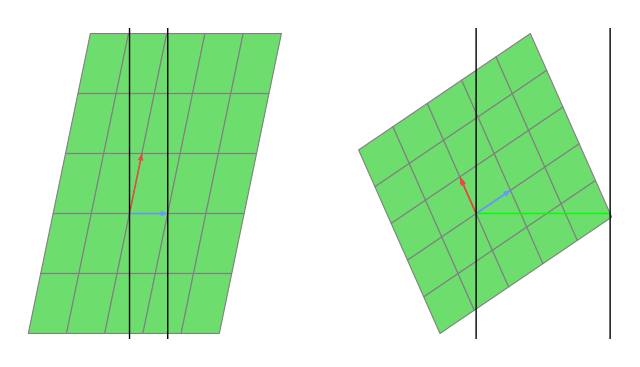

```mathematica
showRenormalisation[{m_,n_},{s_,θ_}] := Module[{u,v,zm,zn,z1,Δ,pm,pn},
{u,v}=euclideanWindingNumberPair[{m,n}]; 
Δ= euclideanDelta[{m,n}];
z1=algebraicForms[m,n,u,v,s,θ,Δ]["z1"];

zm = algebraicForms[m,n,u,v,s,θ,Δ]["zm"];

pm=algebraicForms[m,n,u,v,s,θ,Δ]["pm"];
pn=algebraicForms[m,n,u,v,s,θ,Δ]["pn"];

renorm= algebraicForms[m,n,u,v,s,θ,Δ]["renormalisation"];

diag=makeGrid[θ];

g1=Graphics[{GeometricTransformation[diag,renorm],
InfiniteLine[{0,0},{0,1}],InfiniteLine[{1,0},{0,1}],
 Thick,StandardBlue,Arrow[{{0,0},pm}],
 Thick,StandardRed,Arrow[{{0,0},pn}],
Green,Line[{{0,0},{1,0}}]
}];
g0=Graphics[{diag,
InfiniteLine[{0,0},{0,1}],InfiniteLine[{1,0},{0,1}]
}];
GraphicsRow[{g0,g1}]
];
showRenormalisation[{2,3},{1,2π/5}]
```

```mathematica
euclideanDelta[{4,7}]
```

1

```mathematica
euclideanDelta[{3,4}]
```

-1

```mathematica
zm
```

zm

This generates an m,n chain with width exactly 1. 
The angle that p_m makes with the horizontal is α=Arg[z_m].

```mathematica
Clear[{m,n,u,v}];
gmnAlgebraic[w_] :=(u w - v)/(m w - n);
gmnTrig[s_,θ_] := (v-s u Cos[θ]-ⅈ s u Sin[θ])/(n-m s Cos[θ]-ⅈ m s Sin[θ]);

algebraicRenormalisation[{mNumeric_,nNumeric_}] := Module[{g},

{uNumeric,vNumeric}=euclideanWindingNumberPair[{mNumeric,nNumeric}]; 
m=mNumeric;n=nNumeric;
z1= Δ  (v-s u Cos[θ]-ⅈ s u Sin[θ])/(n-m s Cos[θ]-ⅈ m s Sin[θ]) /. {s->1,θ->latticeAngle,m->mNumeric,n->nNumeric,u->uNumeric,v->vNumeric
, Δ-> euclideanDelta[{mNumeric,nNumeric}]};


z1Coords=ComplexExpand[ReIm[z1]];

pn = n z1Coords - vNumeric {1,0} ;
pm=m z1Coords - uNumeric  {1,0};
z0={1,0};
renorm= RotationTransform[Arg[zm]]@* ScalingTransform[Abs[zm]*{1,1}];
g1=Graphics[{GeometricTransformation[diag,renorm],
InfiniteLine[{-1,0},{0,1}],InfiniteLine[{0,0},{0,1}],InfiniteLine[{1,0},{0,1}],
Thick,
 Blue,Line[{{0,0},pm}],
Green,Line[{{0,0},z0}],
Yellow,Line[{{0,0},pn}]
}];
GraphicsRow[{g1,g0}]
]
algebraicRenormalisation[{2,3}]
```

-Graphics-

```mathematica
m
```

2

```mathematica
z1
```

-(1+1/4 (1-√5)-ⅈ √(5/8+(√5)/8))/(3+1/2 (1-√5)-2 ⅈ √(5/8+(√5)/8))

```mathematica
Simplify@ComplexExpand[gmnAlgebraic[ s Exp[I θ]]]
```

(-v+s u Cos[θ]+ⅈ s u Sin[θ])/(-3+2 s Cos[θ]+2 ⅈ s Sin[θ])

```mathematica
latticeAngle
```

(2 π)/5

```mathematica
gmnAlgebraic[w]
```

(-v+u w)/(-3+2 w)

```mathematica
ComplexExpand[ReIm[gmnAlgebraic[w]]]
```

{-v/(-3+2 w)+(u w)/(-3+2 w),0}

```mathematica
z1OfMNTheta[{m_,n_},θ_]:= Module[{delta,u,v,gFunction,z1},
delta=euclideanDelta[{m,n}];
{u,v}=euclideanWindingNumberPair[{m,n}];
If[m v - n u != delta,Print["cLC ", delta, {m,n},{u,v}]];
gFunction[w_] := (u w - v)/( m w -n);
z1=gFunction[Exp[ I θ]];
delta * z1
];

pmnOfMNTheta[{m_,n_},θ_]:= Module[{z1,u,v,zm,zn},
z1= z1OfMNTheta[{m,n},θ];
{u,v}=euclideanWindingNumberPair[{m,n}];

zm = m z1 - u;
 zn = n z1 - v;
toCartesian [zm+zn]
];
pmOfMNTheta[{m_,n_},θ_]:= Module[{z1,u,v,zm,zn},
z1=z1OfMNTheta[{m,n},θ];
{u,v}=euclideanWindingNumberPair[{m,n}];

zm = m z1 - u;
toCartesian [zm]
];
pnOfMNTheta[{m_,n_},θ_]:= Module[{z1,u,v,zm,zn},
z1= z1OfMNTheta[{m,n},θ];
{u,v}=euclideanWindingNumberPair[{m,n}];

 zn = n z1 - v;
toCartesian [zn]
];

toDelta= (-n u+m v)->Δ;
vIs= Solve[Δ==m v -  n u,v][[1,1]];

toCartesian[z_] :=Module[{x,y,hOverd},
{x,y}= Simplify[ComplexExpand[ReIm[z]]]/. {toDelta,vIs}/. {Δ^2->1};
hOverd=Simplify[Map[Expand,NumeratorDenominator[y/x]]/.  {Δ^2->1}];
<|"h"->y,"d"->x,"h/d"->hOverd|>
];
```

```mathematica
denominator2[w_] :=(m w-n) *( m Conjugate[w] -n);
deltaZ1[w_] := Δ gFunction[w];
cartesiandh = toCartesian[deltaZ1[Subscript[d, 0]+ I Subscript[h, 0]]]
```

<|h→0,d→Δ gFunction[d_0+ⅈ h_0],h/d→{0,1}|>